```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-10;a=1;αSch=2.;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
enV=Flatten@Import["D:\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"]
LδE={{1.3373202085701266,0.33732020857012657},{0.18643393369537004,0.25426426521851986},{0.07105746158595466,0.360482845726408},{0.037407167983470095,0.4014853122644785},{0.023050971424107496,0.42372571439731266},{0.015618389794715332,0.437737967390248},{0.005359292748188737,0.7373946553387517},{0.001293695341342178,0.}};
Lδϵ={{1.3373202085701266,0.5741276779047597},{0.18643393369537004,0.1051516432644786},{0.07105746158595466,0.037300022830719023},{0.037407167983470095,0.0189380005149714},{0.023050971424107496,0.011162659074988026},{0.015618389794715332,0.007167940071927817},{0.005359292748188737,0.0018188435094718296},{0.001293695341342178,0.}};
```

{-1.3373203577743778777484998097,-0.18643394332774011967873561071,-0.071057463765681416850087674062,-0.037407168809596011660801031892,-0.023050971823032012263856091426,-0.01561839001707619878572351763,-0.011277794776154149484804536219,-0.0085243331636150573081138113356,-0.0066688098219347947110873233838,-0.0053592927931919616196373210951,-0.0044008009895061115267162099337,-0.0036782199604481319905959313028,-0.0031200305695982845354571364731,-0.0026798978934000301370515335496,-0.0023267324899791593742692184066,-0.0020390441226088289036420519245,-0.0018015927839557429811049162805,-0.0016033276704600044466081691919,-0.0014360776057045943945272295712,-0.001293695346788560431501052664}

```mathematica
{TimeStamp1,enVs1}=AbsoluteTiming@Module[{min=1.*10^-10,max=2000,sol,ef,evShifted,wpc=30,acg=20},
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+Vs1[r] f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
sol=ParametricNDSolve[{Vs1[r]u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->Infinity,MaxStepFraction->10^-3,WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
(FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]},WorkingPrecision->wpc,AccuracyGoal->acg]&/@evShifted)
]
```

ParametricNDSolve::precw: 微分方程的精度 ({{(-2.81241 Power[«2»]-Power[«2»] Erf[«1»]) u[r$12772]-0.5 u''[r$12772]==e$12771 u[r$12772],u'[2000]==-1.×10^-10,u[2000]==1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::brdig: 根已经被 30. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-20.

General::stop: 在本次计算中，FindRoot::brdig 的进一步输出将被抑制.

{1405.05,{-1.45717100598886308390408496491,-0.186470122851734499721484109663,-0.0711352981987486468595003882349,-0.037425135855293059212614207063,-0.0230565800077264587758491493198,-0.0156205556655882023098559789821,-0.0112787659195096518431231011036,-0.00852481911933151103290077611886,-0.00666907418479170018848404496495,-0.00535944637398260427460713201982,-0.0044008950653956430012969554558,-0.00367828015447274490211939916795,-0.00312007051616471688417553565039,-0.00267992523776271226558119677155,-0.00232675171339076938246526728018,-0.00203905795348731072644326712667,-0.00180160293913611845755075224749,-0.00160333526184545183216605301271,-0.0014360833719742070910647871396,-0.0012936997899031244497736236529}}

```mathematica
enVs1={-1.4571710059888630839040849649137723030807607835960406352236`30.,-0.1864701228517344997214841096627612518725846228901791082015`30.,-0.0711352981987486468595003882349002046830942986100552866098`30.,-0.0374251358552930592126142070629500964718961516313181282961`30.,-0.0230565800077264587758491493198420742301740172399501217459`30.,-0.0156205556655882023098559789821129728925939397535910310241`30.,-0.0112787659195096518431231011035781351962853566326492727998`30.,-0.0085248191193315110329007761188632489108985039245007752975`30.,-0.0066690741847917001884840449649459455131298966180134189302`30.,-0.0053594463739826042746071320198205932722176153628784212493`30.,-0.004400895065395643001296955455798837491259676419248853325`30.,-0.0036782801544727449021193991679488373257750872110422190552`30.,-0.0031200705161647168841755356503866782475130133044924012961`30.,-0.0026799252377627122655811967715492032742451167392264484641`30.,-0.0023267517133907693824652672801764997812954228367842185549`30.,-0.0020390579534873107264432671266655242996368947432685372001`30.,-0.0018016029391361184575507522474867436142182892333231189966`30.,-0.0016033352618454518321660530127070280040509631529406604508`30.,-0.0014360833719742070910647871396039968413463787216456703635`30.,-0.0012936997899031244497736236528983832794771520799184326219`30.};
```

```mathematica
{TimeStamp2,enVs2}=AbsoluteTiming@Module[{min=1.*10^-10,max=2000,sol,ef,evShifted,wpc=30,acg=20},
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+Vs2[r] f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
sol=ParametricNDSolve[{Vs2[r]u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->Infinity,MaxStepFraction->10^-3,WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
(FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]},WorkingPrecision->wpc,AccuracyGoal->acg]&/@evShifted)
]
```

Eigensystem::chnpdef: 警告：可能第一个参数中的第二个矩阵 SparseArray[Automatic,«2»,{1,{{«1»},{«1»}},{0.0266667,-0.00333333,0.00666667,0.00666667,-0.00333333,0.0266667,-0.00333333,0.00666667,0.00666667,-0.00333333,0.0266667,-0.00333333,«79968»,0.00666667,0.00666667,0.0533333,0.00666667,0.00666667,0.0533333,0.00666667,0.00666667,0.0533333,0.00666667,0.0533333}}] 不是正定的，这对于用 Arnoldi 方法给出准确结果是必要的.

ParametricNDSolve::precw: 微分方程的精度 ({{(-2.53643 Power[«2»]+3.26552 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$19470]-0.5 u''[r$19470]==e$19469 u[r$19470],u'[2000]==-1.×10^-10,u[2000]==1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::brdig: 根已经被 30. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-20.

General::stop: 在本次计算中，FindRoot::brdig 的进一步输出将被抑制.

{1516.64,{-1.55584171088430050137124384663,-0.184812889000372187640373356278,-0.0710038755123367237759798801293,-0.0373996869534313416167796101229,-0.0230491129436769083988882616524,-0.0156177565149093328872882035414,-0.0112775314307248250590577027593,-0.00852420772356440515354979501595,-0.00666874384504785851252593055234,-0.00535925537352312102792307008627,-0.00440077846873396008585486393154,-0.00367820574063511393159780775078,-0.00312002122857632600145862255864,-0.00267989154986470808862121769025,-0.00232672805829004744571136991827,-0.00203904094999088382946322758678,-0.00180159046380964435953116602112,-0.00160332594164378861370788677137,-0.00143607629593088660764798821551,-0.00129369433965931994043519199681}}

```mathematica
enVs2={-1.5558417108843005013712438466261869726983033577137417933059`30.,-0.1848128890003721876403733562779198157862165108544619785229`30.,-0.0710038755123367237759798801293111731322135782395477205661`30.,-0.0373996869534313416167796101229189117318876402434724671303`30.,-0.0230491129436769083988882616523797540789066089690857957019`30.,-0.015617756514909332887288203541417676091414345598562136793`30.,-0.0112775314307248250590577027592879625776835870742897081724`30.,-0.0085242077235644051535497950159465365780013990292260390694`30.,-0.0066687438450478585125259305523392745399059230376379391249`30.,-0.0053592553735231210279230700862725790423401776102087543004`30.,-0.0044007784687339600858548639315414253595987954647869009734`30.,-0.0036782057406351139315978077507767296443790198180812079181`30.,-0.0031200212285763260014586225586413216081171160444949654177`30.,-0.0026798915498647080886212176902469595602656128762039619351`30.,-0.0023267280582900474457113699182650080412830289559960992974`30.,-0.0020390409499908838294632275867792789405293272271179377283`30.,-0.0018015904638096443595311660211207929487667719153353650477`30.,-0.0016033259416437886137078867713680926601787412263759926028`30.,-0.0014360762959308866076479882155122895054623198566968706296`30.,-0.0012936943396593199404351919968118797471550396349554513524`30.};
```

```mathematica
δEVs1=Abs[(enVs1-enV)/enV]
δEVs2=Abs[(enVs2-enV)/enV]
```

{0.089619998318088462369977734,0.0001940608204096103156628493,0.0010953730817623364373349704,0.00048031022578855230780540244,0.00024329493513340466033329,0.0001386601634122169838487468,0.0000861111037022726131838976,0.00005700806234650234793939614,0.00003964168479298137709459077,0.0000286569136207210655860288,0.0000213769924511020506088815,0.0000163649877549949049075198,0.0000128032612313449180186688,0.0000102035091521476928519238,8.26197755556350220171001×10^-6,6.78302069507307216672355×10^-6,5.636779002399641533413×10^-6,4.7347685611934479319572×10^-6,4.0152910885810979303998×10^-6,3.4344365348826197408914×10^-6}

{0.163402397817075494934786981,0.00869506002197363827758995974,0.00075415375816684527608008554,0.0002000112920267500525418324,0.00008064212517263651990022353,0.0000405612976864622827969561,0.0000233507910501479615169849,0.0000147155265103407915561068,9.89335259182079286274422×10^-6,6.98220274289302097920422×10^-6,5.11742571526014379479023×10^-6,3.86594960904038551019911×10^-6,2.9938879604428650219068×10^-6,2.3670809763577535632903×10^-6,1.9046835555935580052892×10^-6,1.5559339348748439062117×10^-6,1.2878304793868275663116×10^-6,1.078267560452500897698×10^-6,9.1204939244509307135038×10^-7,7.784902705193617022002×10^-7}

```mathematica
LδEVs1=Transpose@({-enV}~Join~{δEVs1});
LδEVs2=Transpose@({-enV}~Join~{δEVs2});
```

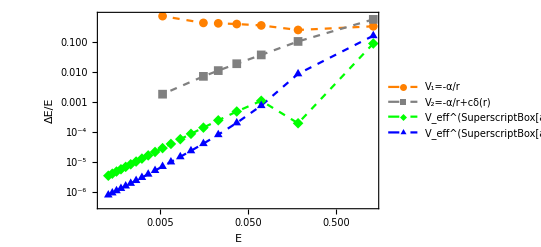

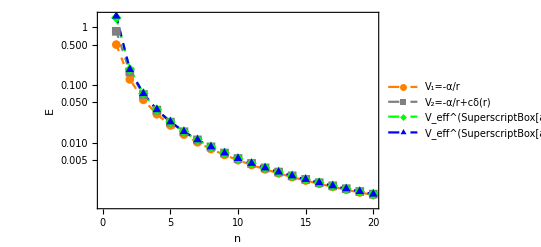

```mathematica
ListLogLogPlot[{LδE,Lδϵ,LδEVs1,LδEVs2},Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","ΔE/E"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->{"V_1=-α/r","V_2=-α/r+cδ(r)","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"}]
Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\Test_PS_CurveFitting_Figure2.eps",%];
ListLogPlot[{Table[1/(2 n^2),{n,20}],-Table[-1/(2 n^2)+-0.6195838082285936/(√π n^3),{n,20}],-enVs1,-enVs2},Frame->True,Joined->True,PlotMarkers->Automatic,FrameLabel->Reverse@{"E","n"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->{"V_1=-α/r","V_2=-α/r+cδ(r)","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},ImageSize->Full]
Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\Test_PS_CurveFitting_Figure2_1.eps",%];
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_enVs1.dat",enVs1,"Table"];
Export["C:\\Users\\ASUS\\Documents\\TestDATA_enVs2.dat",enVs2,"Table"];
```